```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
h=1;
a=0.4;
b=0.3;
c={0.5,0.5};
d=0.1;
```

```mathematica
(*check for mu*)
```

```mathematica
tabf=Import["/Users/michelecastellana/Documents/finite_elements/dynamics/lagrangian_approach/one_dimension/circle/curvature/discontinuous/solution/f.csv"]
tabf=Table[{tabf[[i,2]],tabf[[i,3]]},{i,2,Length[tabf]}]
```

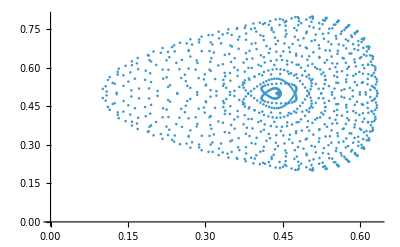

```mathematica
plotf=ListPlot[tabf]
```

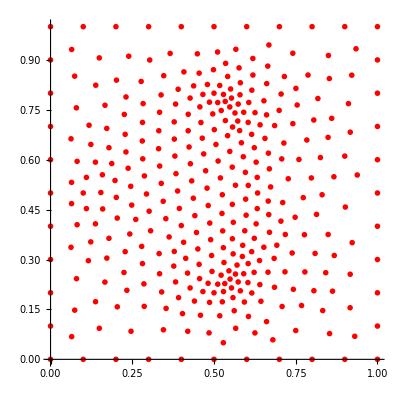

```mathematica
tabve=Import["/Users/michelecastellana/Documents/finite_elements/generate_mesh/2d/square/shape_line/solution/mesh_0/vertices.csv"];
tabve=Table[{tabve[[i,1]],tabve[[i,2]]},{i,2,Length[tabve]}]
plotve=ListPlot[tabve,PlotStyle->{Red,PointSize->0.01},AspectRatio->1]
```

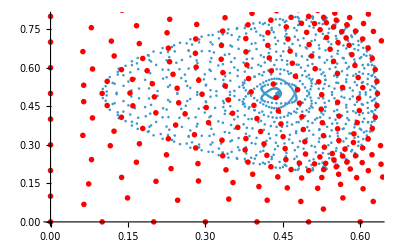

```mathematica
Show[plotf,plotve]
```